```mathematica
eev[cyclelist0_,edge0_]:=EvenQ[Sum[Boole[IntersectingQ[cycle,{edge0}]],{cycle,cyclelist0}]]
```

```mathematica
evcysq[graph_]:=Block[{cyclelist=FindCycle[graph,∞,All],edgelist=EdgeList[graph]},Sum[Boole[eev[cyclelist,edge]],{edge,edgelist}]==Length[edgelist]]
```

```mathematica
evcysq2[graph_]:=Block[{cyclelist=FindCycle[graph,∞,All],edgelist=EdgeList[graph],len=Length[EdgeList[graph]],pos=0,goodsofar=True},
While[pos<len&&goodsofar,pos++;If[¬eev[cyclelist,edgelist[[i]]],goodsofar=False]];goodsofar]
```

```mathematica
goodq[graph_]:=(¬IntersectingQ[EdgeList[graph],{1,2}])&&(SimpleGraphQ[graph])&&(ConnectedGraphQ[graph])
```

```mathematica
firstg=Select[GraphData[3;10],goodq[GraphData[#]]&];
Length[firstg]
secondg=Monitor[monsel[firstg,evcysq2[GraphData[#]]&],{pos,len}];
Length[secondg]
secondg
```

225

Part::partw: Part 29 of {1 <-> 7, 1 <-> 8, 1 <-> 9, 1 <-> 10, 2 <-> 6, 2 <-> 8, 2 <-> 9, 2 <-> 10, 3 <-> 6, 3 <-> 7, 3 <-> 9, 3 <-> 10, 4 <-> 6, 4 <-> 7, 4 <-> 8, 4 <-> 10, 5 <-> 6, 5 <-> 7, 5 <-> 8, 5 <-> 9} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

212

{{Antiprism,5},{Barbell,5},{BlackBishop,{4,5}},{CayleyTree,{3,2}},{Centipede,5},{Circulant,{10,{1,4}}},{Circulant,{10,{1,2,3}}},{Circulant,{10,{1,2,5}}},{Circulant,{10,{1,4,5}}},{Circulant,{10,{1,2,4,5}}},{Complete,10},{CompleteTripartite,{2,4,4}},{Cone,{3,7}},{Cone,{4,6}},{Cone,{5,5}},{Crown,5},{Cubic,{10,1}},{Cubic,{10,2}},{Cubic,{10,3}},{Cubic,{10,4}},{Cubic,{10,5}},{Cubic,{10,6}},{Cubic,{10,7}},{Cubic,{10,8}},{Cubic,{10,9}},{Cubic,{10,10}},{Cubic,{10,11}},{Cubic,{10,12}},{Cubic,{10,13}},{Cubic,{10,14}},{Cubic,{10,16}},{Cubic,{10,18}},{Cycle,10},{DutchWindmill,{3,4}},{Fan,{2,8}},{Fan,{3,7}},{Fan,{4,6}},{Fan,{5,5}},{Firecracker,{2,5}},{Fusene,{2,1}},GolombGraph,{JohnsonSkeleton,15},{JohnsonSkeleton,17},{JohnsonSkeleton,62},{JohnsonSkeleton,64},{JohnsonSkeleton,86},{King,{2,5}},KrackhardtKite,{Ladder,5},{Lollipop,{5,5}},{Lollipop,{6,4}},{Lollipop,{7,3}},{MoebiusLadder,5},{MongolianTent,{3,3}},{Pan,9},PaschGraph,{Path,10},PetersenGraph,{Polyomino,{4,1}},{Polyomino,{4,2}},{Polyomino,{4,3}},{Prism,5},{Quartic,{10,1}},{Quartic,{10,2}},{Quartic,{10,3}},{Quartic,{10,4}},{Quartic,{10,5}},{Quartic,{10,6}},{Quartic,{10,7}},{Quartic,{10,8}},{Quartic,{10,9}},{Quartic,{10,10}},{Quartic,{10,11}},{Quartic,{10,12}},{Quartic,{10,13}},{Quartic,{10,14}},{Quartic,{10,15}},{Quartic,{10,16}},{Quartic,{10,18}},{Quartic,{10,20}},{Quartic,{10,21}},{Quartic,{10,22}},{Quartic,{10,23}},{Quartic,{10,24}},{Quartic,{10,25}},{Quartic,{10,26}},{Quartic,{10,27}},{Quartic,{10,28}},{Quartic,{10,29}},{Quartic,{10,30}},{Quartic,{10,31}},{Quartic,{10,32}},{Quartic,{10,33}},{Quartic,{10,34}},{Quartic,{10,35}},{Quartic,{10,36}},{Quartic,{10,37}},{Quartic,{10,38}},{Quartic,{10,39}},{Quartic,{10,40}},{Quartic,{10,41}},{Quartic,{10,42}},{Quartic,{10,43}},{Quartic,{10,44}},{Quartic,{10,45}},{Quartic,{10,46}},{Quartic,{10,47}},{Quartic,{10,48}},{Quartic,{10,49}},{Quartic,{10,50}},{Quartic,{10,51}},{Quartic,{10,52}},{Quartic,{10,53}},{Quartic,{10,54}},{Quartic,{10,55}},{Quartic,{10,56}},{Quartic,{10,57}},{Queen,{2,5}},{Quintic,{10,1}},{Quintic,{10,2}},{Quintic,{10,4}},{Quintic,{10,5}},{Quintic,{10,6}},{Quintic,{10,7}},{Quintic,{10,8}},{Quintic,{10,9}},{Quintic,{10,10}},{Quintic,{10,11}},{Quintic,{10,12}},{Quintic,{10,14}},{Quintic,{10,15}},{Quintic,{10,16}},{Quintic,{10,17}},{Quintic,{10,18}},{Quintic,{10,19}},{Quintic,{10,20}},{Quintic,{10,21}},{Quintic,{10,22}},{Quintic,{10,23}},{Quintic,{10,24}},{Quintic,{10,25}},{Quintic,{10,26}},{Quintic,{10,27}},{Quintic,{10,28}},{Quintic,{10,29}},{Quintic,{10,30}},{Quintic,{10,31}},{Quintic,{10,32}},{Quintic,{10,33}},{Quintic,{10,34}},{Quintic,{10,35}},{Quintic,{10,36}},{Quintic,{10,37}},{Quintic,{10,38}},{Quintic,{10,39}},{Quintic,{10,40}},{Quintic,{10,41}},{Quintic,{10,42}},{Quintic,{10,43}},{Quintic,{10,44}},{Quintic,{10,45}},{Quintic,{10,46}},{Quintic,{10,47}},{Quintic,{10,48}},{Quintic,{10,49}},{Quintic,{10,50}},{Quintic,{10,51}},{Quintic,{10,52}},{Quintic,{10,53}},{Quintic,{10,54}},{Quintic,{10,55}},{Quintic,{10,56}},{Quintic,{10,57}},{Quintic,{10,58}},{Septic,{10,1}},{Septic,{10,2}},{Septic,{10,4}},{Sextic,{10,1}},{Sextic,{10,2}},{Sextic,{10,3}},{Sextic,{10,4}},{Sextic,{10,5}},{Sextic,{10,6}},{Sextic,{10,9}},{Sextic,{10,10}},{Sextic,{10,11}},{Sextic,{10,12}},{Sextic,{10,13}},{Sextic,{10,14}},{Sextic,{10,15}},{Sextic,{10,16}},{Sextic,{10,17}},{Sextic,{10,21}},{Star,10},{Sun,5},{Sunlet,5},{Tadpole,{5,5}},{Tadpole,{6,4}},{Tadpole,{7,3}},{TorusGrid,{4,6}},{TorusGrid,{5,5}},{Triangular,5},{TriangularGrid,3},{TriangularHoneycombQueen,4},{Turan,{10,4}},{Turan,{10,6}},{Turan,{10,7}},{Turan,{10,8}},{Turan,{10,9}},{Wheel,10},{WhiteBishop,{3,7}},{Windmill,{3,4}}}

```mathematica
monsel[list_,cond_]:=Map[First,Select[Monitor[Table[{list[[i]],cond[list[[i]]]},{i,1,Length[list]}],i],TrueQ[Last[#]]&]]
```

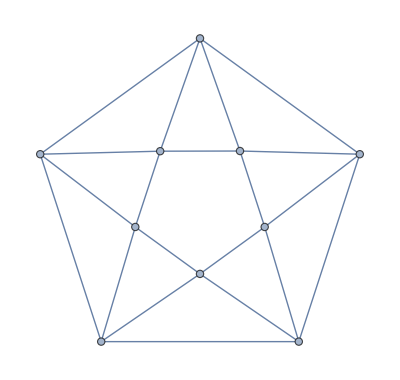
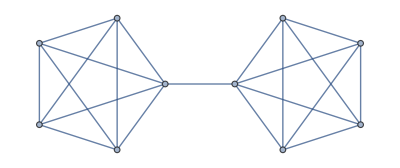
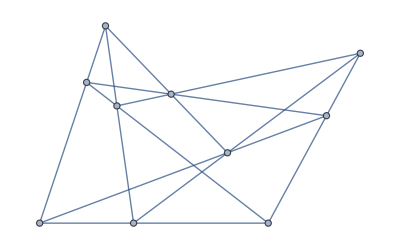
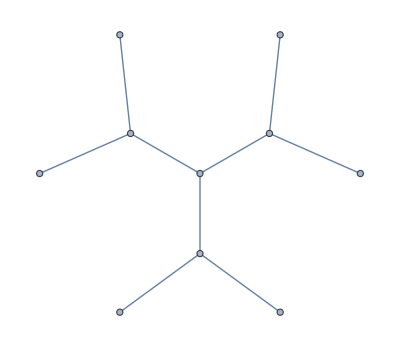
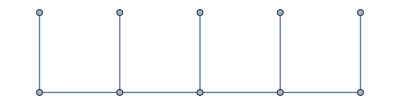
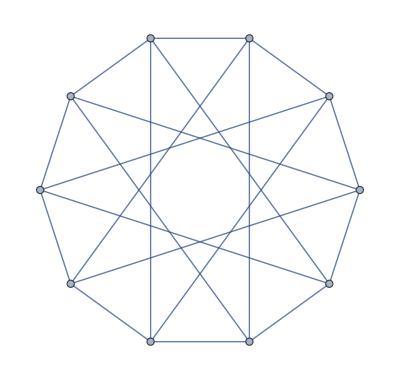
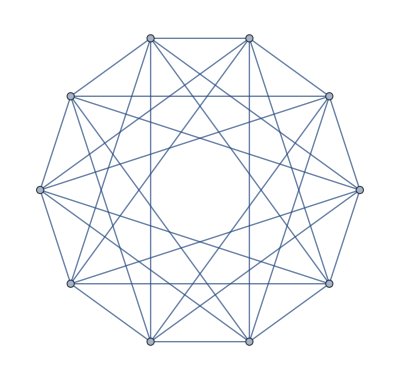
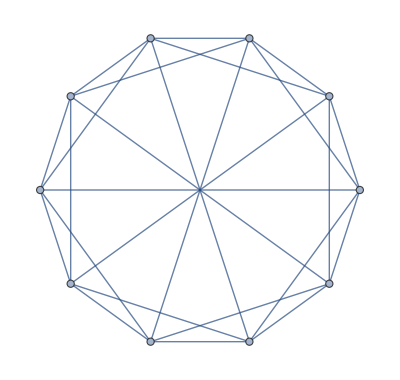
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[GraphData,Out[36]]
```

```mathematica
Map[GroupOrder[GraphAutomorphismGroup[GraphData[#]]]&,Out[36]]
```

{20,1152,2,48,2,320,20,20,320,20,3628800,2304,30240,5760,1200,240,32,16,4,8,16,2,4,4,8,12,6,6,2,48,4,8,20,48,4,12,48,240,72,4,6,16,16,4,6,4,64,2,4,24,120,720,20,2,2,24,2,120,2,1,2,20,144,64,8,4,8,8,12,48,4,4,16,2,8,2,16,2,8,2,4,1,4,4,2,2,2,2,4,1,1,2,2,32,2,2,2,4,1,4,2,8,4,4,4,4,4,2,2,16,2,16,16,2,10,4,8,4,8,4,32,8,2,8,16,8,4,8,16,4,4,48,4,12,2,2,2,2,2,2,1,1,4,4,16,2,2,4,2,16,4,2,1,4,1,2,16,8,2,4,2,2,2,2,2,8,4,144,16,4,4,4,10,64,96,576,84,1728,16,48,4,32,6,4,4,2,4,8,8,2,8,16,6,362880,10,10,2,2,2,96,200,120,6,12,576,768,1152,5760,80640,18,4,1296}

```mathematica
Map[GraphData,Select[Out[36],GroupOrder[GraphAutomorphismGroup[GraphData[#]]]==1&]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}